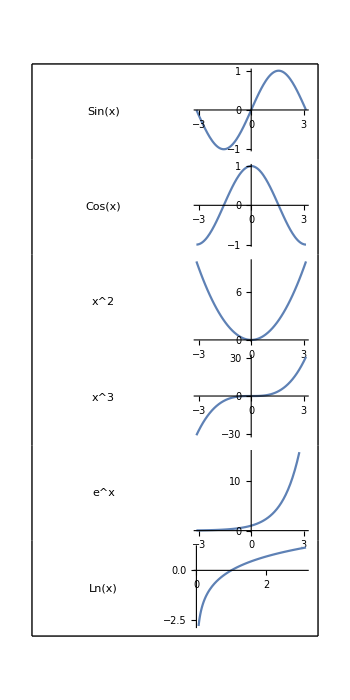

```mathematica
graph1 = GraphicsGrid[List[{"Sin(x)", Plot[Sin[x], {x,-Pi,Pi}]}, {"Cos(x)", Plot[Cos[x], {x,-Pi,Pi}]}, {"x^2", Plot[x^2, {x,-Pi,Pi}]}, {"x^3", Plot[x^3, {x,-Pi,Pi}]}, {"e^x", Plot[E^x, {x,-Pi,Pi}]}, {"Ln(x)", Plot[Log[x], {x,0,Pi}]}], Frame->True, Spacings->{Automatic, 3}, ImageSize->{350,700}]
```

```mathematica
graph1
```

-Graphics-

```mathematica
Rasterize[graph1,"Image"]
```

-Graphics-

```mathematica
Export["/home/nathan/QEA/HW1/graph1.png",%91,"PNG"]
```

/home/nathan/QEA/HW1/graph1.png